## adaptive control of unstable 1st-order system (Figure 10.1)

```mathematica
Clear["Global`*"];
```

```mathematica
adapt[γ_,x0_,τ_,k0_,α_,ad_,ωd_]:=Module[{eqs,init,pars,x,t,a,u,j,k},
eqs={x'[t]- a x[t]==u[t]+ad UnitStep[t-10] Sin[ωd t],u[t]==-k[t]x[t-τ],k'[t]==γ x[t]^2-α k[t],j'[t]==1/2(x[t]^2+u[t]^2)};
init={x[t /; t ≤ 0]==x0 ,k[t /; t ≤ 0]==k0,j[0 ]==0,u[t /; t ≤ 0]==-k[t /; t ≤ 0]x[t /; t ≤ 0]};

NDSolveValue[{eqs,init}/.a->1,
{x,u,k,j},{t,0,tend},MaxSteps->10^5]//Quiet]
```

An adaptive gain will stabilize the system, no matter what the value of a.

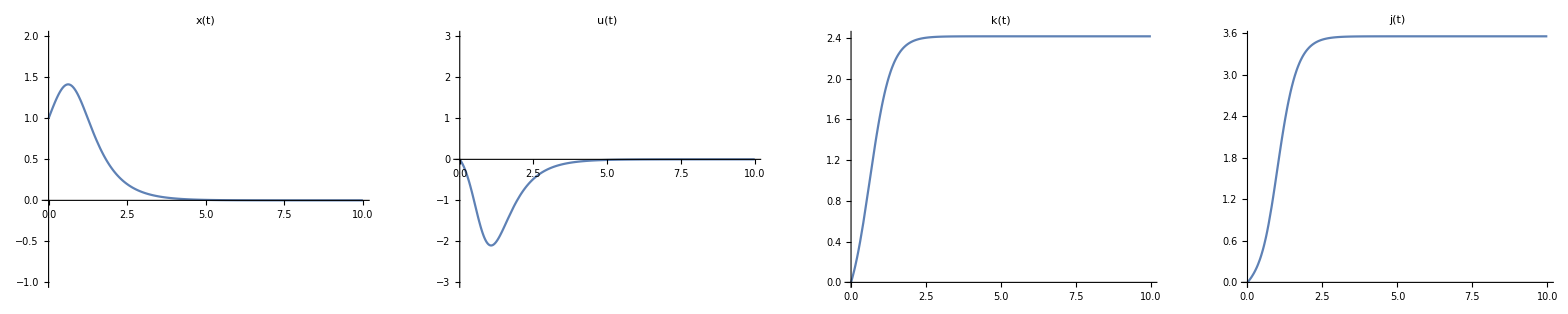

```mathematica
tend=10;γ=1; x0=1;
{xs,us,ks,js}=adapt[γ,x0,0,0,0,0,0];p1=Plot[xs[t],{t,0,tend},PlotRange->{-1,2},PlotLabel->"x(t)"]; 
p2=Plot[us[t],{t,0,tend},PlotRange->{-3,3},PlotLabel->"u(t)"]; 
p3=Plot[ks[t],{t,0,tend},PlotRange->{0,Automatic},PlotLabel->"k(t)"];
p4=Plot[js[t],{t,0,tend},PlotRange->{0,Automatic},PlotLabel->"j(t)"];

GraphicsRow[{p1,p2,p3,p4},ImageSize->Full]
```

A continuing disturbance causes the gain k(t) to steadily increase.

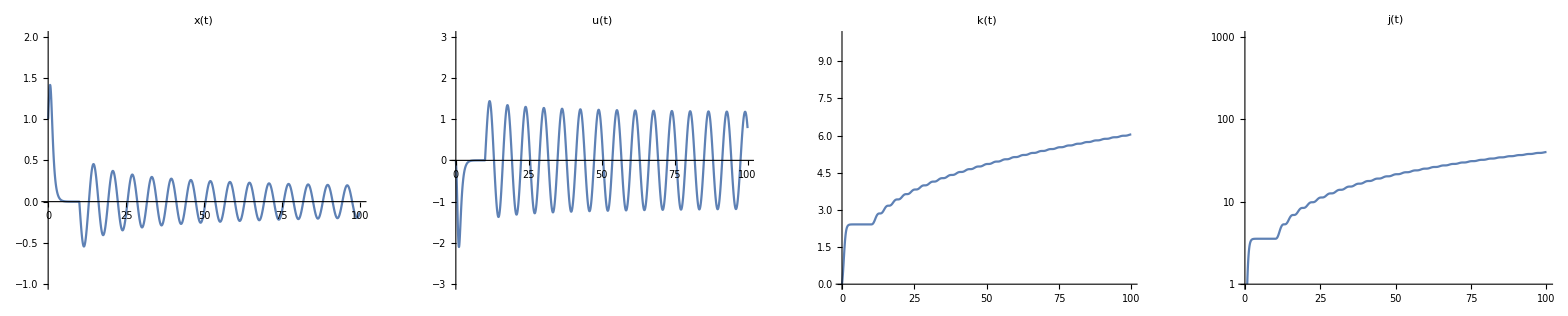

```mathematica
tend=100; ad=1; ωd=1;{xs1,us1,ks1,js1}=adapt[γ,x0,0,0,0,ad,ωd];p5=Plot[xs1[t],{t,0,tend},PlotRange->{-1,2},PlotLabel->"x(t)"]; 
p6=Plot[us1[t],{t,0,tend},PlotRange->{-3,3},PlotLabel->"u(t)"]; 
p7=Plot[ks1[t],{t,0,tend},PlotRange->{0,10},PlotLabel->"k(t)"];
p8=LogPlot[js1[t],{t,0,tend},PlotRange->{1,1000},PlotLabel->"j(t)"];

GraphicsRow[{p5,p6,p7,p8},ImageSize->Full]
```

A delay applying feedback causes instability when the gain is too high.

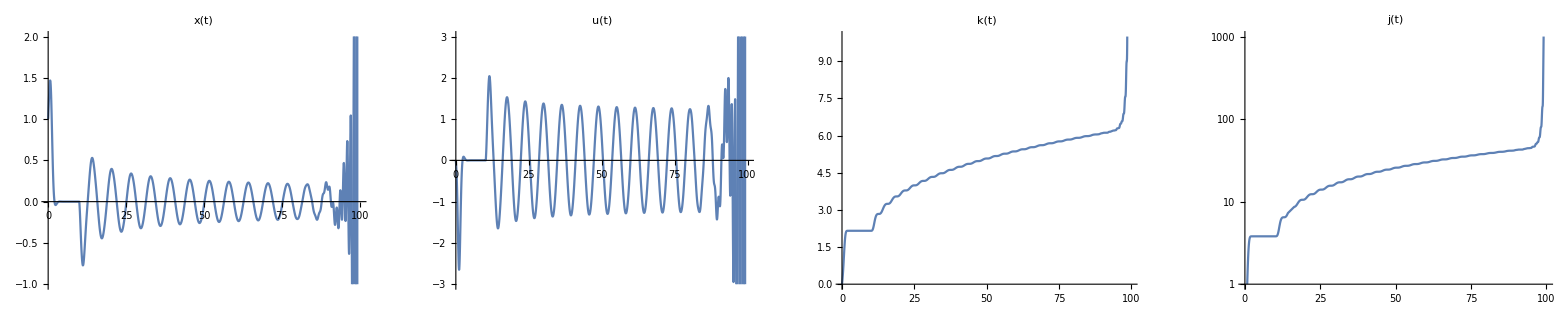

```mathematica
tend=100; τ=0.265;{xs2,us2,ks2,js2}=adapt[γ,x0,τ,0,0,ad,ωd];p9=Plot[xs2[t],{t,0,tend},PlotRange->{-1,2},PlotLabel->"x(t)"]; 
p10=Plot[{us2[t]},{t,0,tend},PlotRange->{-3,3},PlotLabel->"u(t)"]; 
p11=Plot[ks2[t],{t,0,tend},PlotRange->{0,10},PlotLabel->"k(t)"];
p12=LogPlot[js2[t],{t,0,tend},PlotRange->{1,1000},PlotLabel->"j(t)"];

GraphicsRow[{p9,p10,p11,p12},ImageSize->Full]
```

Export data

```mathematica
dt=0.1; 
tend=10;         dat1=Table[Through[{xs,us,ks,js}[t]],{t,0,tend,dt}];
tend=100;       dat2=Table[Through[{xs1,us1,ks1,js1}[t]],{t,0,tend,dt}];
tend=99.3;     dat3=Table[Through[{xs2,us2,ks2,js2}[t]],{t,0,tend,dt}];
(* 
SetDirectory[NotebookDirectory[]];
Export["unstableAdapt1a.dat",dat1];
Export["unstableAdapt1b.dat",dat2];
Export["unstableAdapt1c.dat",dat3]; 
*)
```

Addendum:  How does the asymptotic value of j depend on k0?  (It’s complicated; no clear trends.)

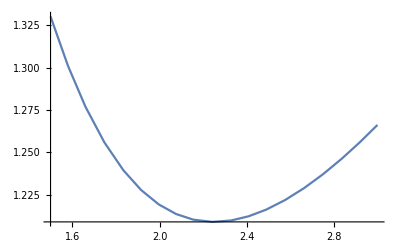

```mathematica
adapt1[γ_,x0_,τ_,k0_,α_,ad_,ωd_]:=Module[{eqs,init,pars,x,t,a,u,j,k,xs,ks,us,js},
eqs={x'[t]- a x[t]==u[t]+ad UnitStep[t] Sin[ωd t],u[t]==-k[t]x[t-τ],k'[t]==γ x[t]^2-α k[t],j'[t]==1/2(x[t]^2+u[t]^2)};
init={x[t /; t ≤ 0]==x0 ,k[t /; t ≤ 0]==k0,j[0 ]==0,u[t /; t ≤ 0]==-k[t /; t ≤ 0]x[t /; t ≤ 0]};

{xs,ks,us,js}=NDSolveValue[{eqs,init}/.a->1,
{x,u,k,j},{t,0,tend},MaxSteps->10^5]//Quiet;js[tend]]

tend=10;
Plot[adapt1[1,1,0,k0,0,0,5],{k0,1.5,3},MaxRecursion->1,PlotPoints->10]
```